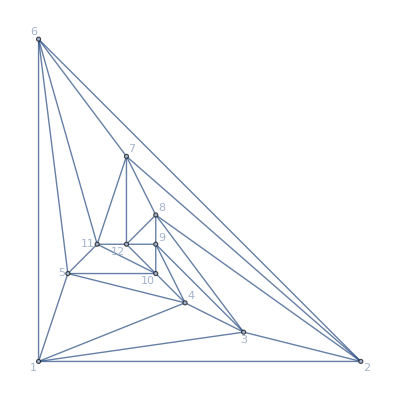

```mathematica
Graph[plantri[[1]],GraphLayout->"PlanarEmbedding", VertexLabels->Automatic]
```

```mathematica
Table[ChromaticPolynomial[CompleteGraph[k],4],{k,5}]
```

{4,12,24,24,0}

```mathematica
ZykovDecomposition4[g_Graph,vertices_List,count_]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,g2},
g2=Graph[g,VertexLabels->Map[#->#&,VertexList[g]]];
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g2,split[[1]]];
right=VertexDelete[g2,split[[2]]];
middle=VertexDelete[g2,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Monitor[
Total[Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
ChromaticPolynomial[lefta,4]*ChromaticPolynomial[righta,4]/ChromaticPolynomial[middlea,4],
{sol,Select[sols,Length[#]==count&]}
]],
sol]
]
```

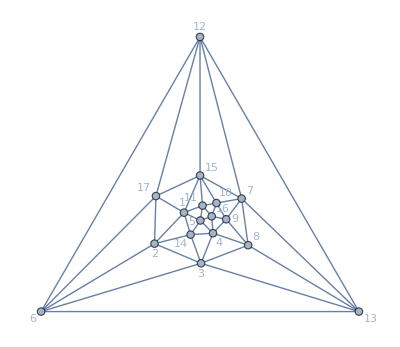

```mathematica
plantri8
```

```mathematica
Table[ZykovDecomposition4[Graph[plantri[[1]],GraphLayout->"PlanarEmbedding", VertexLabels->Automatic],{1,3,9,12,11,5},k],{k,2,4}]
```

{0,96,144}

```mathematica
Table[ZykovDecomposition4[plantri8,{1,14,4,16,11},k],{k,2,4}]
```

{0,528,0}

```mathematica
Table[ZykovDecomposition4[plantri8,{7,8,9,4,5,1,15},k],{k,2,4}]
```

{0,0,528}

```mathematica
Table[ZykovDecomposition4[plantri8,{1,2,3,4,5},k],{k,2,4}]
```

{0,528,0}

```mathematica
Table[ZykovDecomposition4[plantri8,{1,2,3,8,4,5},k],{k,2,4}]
```

{0,144,384}

```mathematica
Total[{0,144,384}]
```

528